# Response Function- Helion 19/02/24

[σ_tot]=μb=10^-4 fm^2
[σ_tot]=mb=10^-1 fm^2
[Lab photon energy] = MeV

```mathematica
dbg=False;
```

#### set of regulator functions to smooth the discrete result of the inverse Lorentz transfrom

```mathematica
Off[Inverse::luc,General::munfl,FindFit::lstol,ClebschGordan::phy,LinearSolve::luc]
Needs["MaTeX`"]
texStyle={FontFamily->"Latin Modern Roman",FontSize->12};
SetOptions[MaTeX,"Preamble"->{"\\usepackage{color,txfonts}"}];

readREAL8list[fn_,freal_:"Real64",finteger_:"Integer32"]:=Block[{str,headmarker,data},
str=OpenRead[fn,BinaryFormat->True];
headmarker=BinaryRead[str,finteger,ByteOrdering->$ByteOrdering];
data=BinaryReadList[str,freal,ByteOrdering->$ByteOrdering];
Close[str];
data];

trafoToIDNorm[normMat_]:=Block[{dbg=True},
{evaln,evecn}=Eigensystem[normMat];

diagev=DiagonalMatrix[evaln^(-0.5)];
fulltrafo=Transpose[evecn].diagev;
fulltrafo
];
```

```mathematica
multipolarity=1;
mLs=Range[-multipolarity,multipolarity,1];

parity="-";
Subscript[I, n]={0.5,1.5}; (*Spin of Excited states*)
J0=0.5; (*Spin of Ground states which consists of two channels s and d*)
mIns=Range[-#,#,1]&/@Subscript[I, n];
lege="J_lit="<>ToString[#]&/@Subscript[I, n];
thresholdLIT=(10.)^(-5);
dH=1; (* this takes only every dH basis vector into account; ECCE: not benchmarked *)
```

```mathematica
ImgSize=900;
mnucl=938.3;
hbarc=197.3269804; (*codata*)

hbarsqO2m=hbarc^2/(2 mnucl);
(*αfine=1./137.*)
αfine=UnitConvert[Quantity[1,"FineStructureConstant"]];
hat[l_]:=Sqrt[2 l+1];

resultsDir="/home/kirscher/scratch/compton_IRS/testrun";

files=FileNames[All,resultsDir];
anzBas=Length[Select[files,StringMatchQ[#,"*mat*BasNR*"]&]]/Length[Subscript[I, n]];

SetDirectory[resultsDir];
dt=ToString[Import["dtype.dat"][[1]][[1]]];
datatype="Real64";
Which[dt=="float32",datatype="Real32",dt=="float64",datatype="Real64"];
Print["Read FORTRAN results from \n",Style[resultsDir,18,Red],"\nin\n",Style[dt,18,Red],"=",Style[datatype,18,Red],"\nformat for\nN_bases=",Style[anzBas,18,Red],"\nevolved bases for the expansion of the final state."];
```

Read FORTRAN results from 
/home/kirscher/scratch/compton_IRS/testrun
in
float64=Real64
format for
N_bases=3
evolved bases for the expansion of the final state.

### Read H_nm:=⟨n|(Ĥ)_(V18+UIX)|m⟩ and 𝕟_nm:=⟨n|OverHat[𝟙]|m⟩≠𝟙_nm

```mathematica
DNormHamMat=readREAL8list["./mat_npp0.5^+"];
tmp=DNormHamMat[[Range[1,Length[DNormHamMat],2]]];

DBasisDim=IntegerPart[Sqrt[Length[DNormHamMat] 0.5]];
Print["Helion-basis Dimension = ",DBasisDim];

DNorm=ArrayReshape[DNormHamMat[[1;;DBasisDim^2]],{DBasisDim,DBasisDim}][[;;;;dH,;;;;dH]];
DHam=ArrayReshape[DNormHamMat[[DBasisDim^2+1;;]],{DBasisDim,DBasisDim}][[;;;;dH,;;;;dH]];
```

Helion-basis Dimension = 426

transform this basis s.t. one can safely “insert 𝟙”:

```mathematica
fulltrafonm=trafoToIDNorm[DNorm];

If[dbg,
Print[ArrayRules[SparseArray[Chop[Transpose[fulltrafonm].DNorm.fulltrafonm]]]];Print[fulltrafonm//MatrixForm];
Print[Chop[Transpose[fulltrafonm].DNorm.fulltrafonm]//MatrixForm];
Print[DNorm//MatrixForm];];
```

#### The initial state (Helion ground state D )

other parts of this section yield analytic information on the initial state

```mathematica
orderedEVDp=Sort[Transpose[Eigensystem[{DHam,DNorm}]],Re[#1[[1]]]<Re[#2[[1]]]&];
evalGSp=orderedEVDp[[1]][[1]]
evecGSp=orderedEVDp[[1]][[2]];
Norm[evecGSp]
orderedEVD=Sort[Transpose[Eigensystem[Transpose[fulltrafonm].DHam.fulltrafonm]],Re[#1[[1]]]<Re[#2[[1]]]&];
evalGS=orderedEVD[[1]][[1]];
evecGS=orderedEVD[[1]][[2]];
Norm[evecGS]
RealDigits[evalGSp,10,6]==RealDigits[evalGS,10,6]
```

-7.58247

1.

1.

True

### Read H_αβ^J:=⟨α|(Ĥ)_(V18+UIX)|β⟩ and 𝕟_αβ^J:=⟨α|OverHat[𝟙]|β⟩

the matrices are obtained with the FORTRAN implementation and employ normalized but non-orthogonal basis vectors.
the quantum numbers of the states m are those of the final state, i.e., J^π=(0)^- or J^π=(1)^- or J^π=(2)^- for the negative-parity rank-1 E_1 operator perturbing a Helion;

```mathematica
matnames=FileNames["mat_*^-_BasNR-*"];
matnamesJ=Table[Select[matnames,StringMatchQ[#,"*"<>ToString[Subscript[I, n][[Inn]]]<>"*"]&],{Inn,Range[Length[Subscript[I, n]]]}];

FSNormHamMat=Table[readREAL8list[#]&/@Sort[matnamesJ[[Inn]],ToExpression[StringSplit[#1,"-"][[-1]]]<ToExpression[StringSplit[#2,"-"][[-1]]]&],{Inn,Range[Length[Subscript[I, n]]]}];

FSbasisDim=Table[IntegerPart[Sqrt[Length[#] 0.5]]&/@FSNormHamMat[[Inn]],{Inn,Range[Length[Subscript[I, n]]]}];

Print["Final-state-basis Dimension = ",FSbasisDim];
FSNorm=Table[ArrayReshape[FSNormHamMat[[Inn]][[#]][[1;;FSbasisDim[[Inn]][[#]]^2]],{FSbasisDim[[Inn]][[#]],FSbasisDim[[Inn]][[#]]}][[;;;;dH,;;;;dH]]&/@Range[anzBas],{Inn,Range[Length[Subscript[I, n]]]}];
FSHam=Table[ArrayReshape[FSNormHamMat[[Inn]][[#]][[FSbasisDim[[Inn]][[#]]^2+1;;]],{FSbasisDim[[Inn]][[#]],FSbasisDim[[Inn]][[#]]}][[;;;;dH,;;;;dH]]&/@Range[anzBas],{Inn,Range[Length[Subscript[I, n]]]}];
```

Final-state-basis Dimension = {{321,327,306},{350,340,334}}

transform this basis s.t. one can safely “insert 𝟙”:

```mathematica
fulltrafosαβ=Table[trafoToIDNorm[FSNorm[[Inn]][[#]]]&/@Range[anzBas],{Inn,Range[Length[Subscript[I, n]]]}];
If[dbg,Print[ArrayRules[SparseArray[Chop[Transpose[fulltrafosαβ[[1]][[1]]].FSNorm[[1]][[1]].fulltrafosαβ[[1]][[1]]]]];fulltrafosαβ[[1]][[1]]//MatrixForm]];
```

#### The final states

```mathematica
esysFSp=Table[Sort[Transpose[Eigensystem[{FSHam[[Inn]][[Nbb]],FSNorm[[Inn]][[Nbb]]}]],Re[#1[[1]]]<Re[#2[[1]]]&],{Inn,Range[1,Length[Subscript[I, n]]]},{Nbb,Range[anzBas]}];
esysFSp[[2]][[1]][[1;;5,1]]
Norm[esysFSp[[1]][[1]][[1,2]]];
FSDimp=Table[Length[esysFSp[[Inn]][[Nbb]][[1]][[2]]],{Inn,Range[1,Length[Subscript[I, n]]]},{Nbb,Range[anzBas]}]
```

{-1.57379,-0.801792,0.247783,0.286037,0.51637}

{{321,327,306},{350,340,334}}

```mathematica
esysFS=Table[Sort[Transpose[Eigensystem[Transpose[fulltrafosαβ[[Inn]][[Nbb]]].FSHam[[Inn]][[Nbb]].fulltrafosαβ[[Inn]][[Nbb]]]],Re[#1[[1]]]<Re[#2[[1]]]&],{Inn,Range[1,Length[Subscript[I, n]]]},{Nbb,Range[anzBas]}];
esysFS[[2]][[2]][[1;;5,1]]
FSDim=Table[Length[esysFS[[Inn]][[Nbb]][[1]][[2]]],{Inn,Range[1,Length[Subscript[I, n]]]},{Nbb,Range[anzBas]}]
Norm[esysFS[[1]][[1]][[1,2]]];
```

{-1.56157,-0.605411,0.244367,0.440878,0.518712}

{{321,327,306},{350,340,334}}

#### Read RHS ⟨α|O_Lm_L|n⟩

the calculation is parallel in n_k parts

```mathematica
CouplingBlockjAs={};

Do[
If[Sign[Subscript[I, n][[nj]]]>=0,JLIT=StringPadRight[StringDelete[ToString[Subscript[I, n][[nj]]],"."],2,"0"],JLIT=StringPadRight[StringDelete[ToString[Subscript[I, n][[nj]]],"."],3,"0"]];

CouplingBlockjA={};

Do[

CouplingBlock={};
CouplingBlockTA={};

Do[
mM=Select[mLs,ClebschGordan[{multipolarity,#},{J0,mIn-#},{Subscript[I, n][[nj]],mIn}]≠0&];
	(*Why is mM unused here *)
fntmp = "InMIn_"<>ToString[Subscript[I, n][[nj]]]<>"_"<>ToString[mIn]<>"_BasNR-"<>ToString[nb]<>"."<>dt;
tmp =BinaryReadList[fntmp,datatype];

OutDim=Dimensions[tmp][[1]]/DBasisDim;
Print[OutDim];

test=ArrayReshape[tmp,{OutDim,DBasisDim}][[;;;;dH,;;;;dH]];
AppendTo[CouplingBlockTA,{mIn,test}];

,{mIn,mIns[[nj]]}];

AppendTo[CouplingBlockjA,CouplingBlockTA];

,{nb,Range[anzBas]}];

AppendTo[CouplingBlockjAs,CouplingBlockjA];

,{nj,Range[1,Length[Subscript[I, n]]]}];

Print["Dim(⟨ψ|ο̂|D⟩) = ",Table[Dimensions[CouplingBlockjAs[[Inn]][[#]][[1]][[2]]]&/@Range[anzBas],{Inn,Range[1,Length[Subscript[I, n]]]}]];
Print["Dim(⟨ψ|Ĥ|ψ⟩) = ",Table[Dimensions[FSHam[[Inn]][[#]]]&/@Range[anzBas],{Inn,Range[1,Length[Subscript[I, n]]]}]];
Print["Dim(⟨ψ|OverHat[1]|ψ⟩) = ",Table[Dimensions[FSNorm[[Inn]][[#]]]&/@Range[anzBas],{Inn,Range[1,Length[Subscript[I, n]]]}]];
```

321

321

327

327

306

306

350

350

350

«1 more identical outputs»

340

340

340

«1 more identical outputs»

334

334

334

«1 more identical outputs»

Dim(⟨ψ|ο̂|D⟩) = {{{321,426},{327,426},{306,426}},{{350,426},{340,426},{334,426}}}

Dim(⟨ψ|Ĥ|ψ⟩) = {{{321,321},{327,327},{306,306}},{{350,350},{340,340},{334,334}}}

Dim(⟨ψ|OverHat[1]|ψ⟩) = {{{321,321},{327,327},{306,306}},{{350,350},{340,340},{334,334}}}

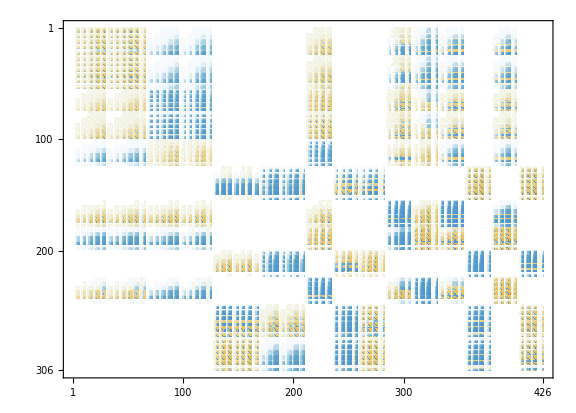
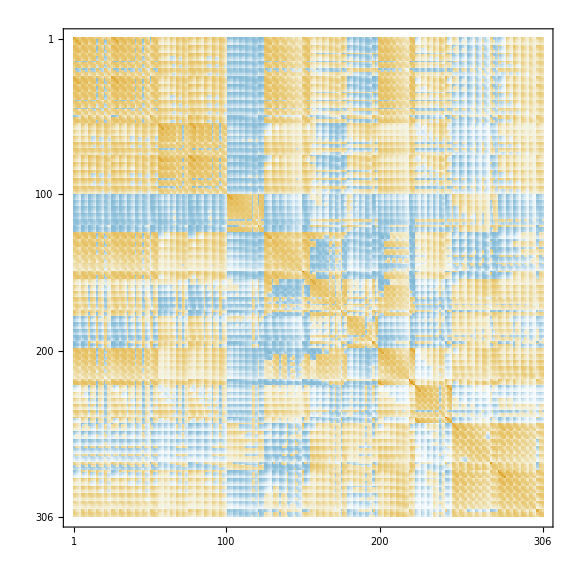
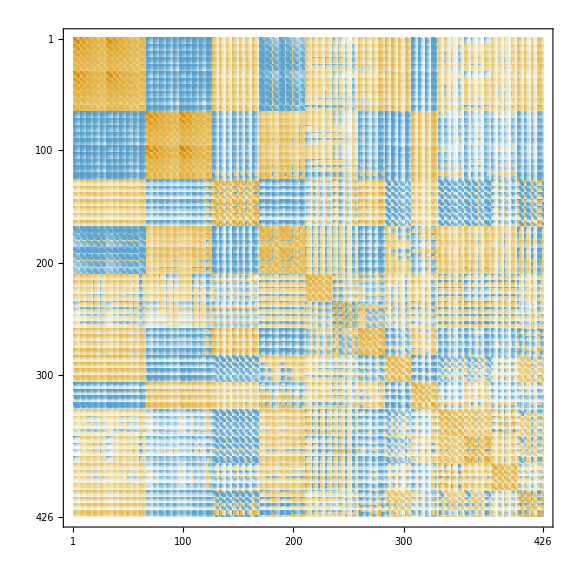
-Graphics- | 
-Graphics- | -Graphics-

```mathematica
nj=1;nb=3;
Grid[{{
MatrixPlot[Chop[CouplingBlockjAs[[nj]][[nb]][[1]][[2]]],FrameLabel->{MaTeX["E1\\otimes{}^3\\text{He Basis-vector}",Magnification->2],MaTeX["{}^3\\text{He Basis-vector}",Magnification->2]},PlotLabel->MaTeX["\\text{Optimal Coupling}",Magnification->2],ImageSize->Large]
},{
MatrixPlot[Chop[FSHam[[nj]][[nb]]],FrameLabel->{MaTeX["E1\\otimes{}^3\\text{He Basis-vector}",Magnification->2],MaTeX["E1\\otimes{}^3\\text{He Basis-vector}",Magnification->2]},PlotLabel->MaTeX["\\text{Final-state Hamiltonian}",Magnification->2],ImageSize->Large]
,
MatrixPlot[Chop[DHam],FrameLabel->{MaTeX["{}^3\\text{He Basis-vector}",Magnification->2],MaTeX["{}^3\\text{He Basis-vector}",Magnification->2]},PlotLabel->MaTeX["\\text{D Hamiltonian}",Magnification->2],ImageSize->Large]
}}]
```

#### Analysis of RHS

```mathematica
inhomoEBp=Table[{},{nj,Length[Subscript[I, n]]}];
inhomoEB=Table[{},{nj,Length[Subscript[I, n]]}];
Do[(* final-state-J loop *)
Do[(* basis-scenario loop *)
Do[(* Subscript[m, L] loop *)
tmpt=Transpose[fulltrafosαβ[[nj]][[nb]]].CouplingBlockjAs[[nj]][[nb]][[mm]][[2]].fulltrafonm;
tmpf=Table[{
esysFS[[nj]][[nb]][[nfs]][[1]],
αfine/4.5 (esysFS[[nj]][[nb]][[nfs]][[2]].tmpt.evecGS)^2
},{nfs,1,FSDim[[nj]][[nb]]}];

AppendTo[inhomoEB[[nj]],tmpf];

tmp=CouplingBlockjAs[[nj]][[nb]][[mm]][[2]];
tmpg=Table[{
esysFSp[[nj]][[nb]][[nfs]][[1]],
αfine/4.5 (esysFS[[nj]][[nb]][[nfs]][[2]].tmp.evecGS)^2
},{nfs,1,FSDimp[[nj]][[nb]]}];

AppendTo[inhomoEBp[[nj]],tmpg];
,{mm,Range[1,Length[mIns[[nj]]]]}
];
,{nb,Range[anzBas]}
];
,{nj,Range[1,Length[Subscript[I, n]]]}
];
fns=Table[Transpose[{inhomoEB[[Inn]][[nbb]][[All,1]],Accumulate[inhomoEB[[Inn]][[nbb]][[All,2]]]}],{Inn,Range[1,Length[Subscript[I, n]]]},{nbb,Range[anzBas]}];
fnsp=Table[Transpose[{inhomoEBp[[Inn]][[nbb]][[All,1]],Accumulate[inhomoEBp[[Inn]][[nbb]][[All,2]]]}],{Inn,Range[1,Length[Subscript[I, n]]]},{nbb,Range[anzBas]}];
Grid[{{ListPlot[fnsp[[1]],PlotRange->{{0,10^3},All},ImageSize->Large,Frame->True,PlotRangePadding->0,FrameLabel->{"E_rel (MeV)","∫F_J (fm)"},LabelStyle->Large,Joined->True,PlotLegends->{"J^π=(1/2)^-"}],
ListPlot[fnsp[[2]],PlotRange->{{0,10^3},All},ImageSize->Large,Frame->True,PlotRangePadding->0,FrameLabel->{"E_rel (MeV)","∫F_J (fm)"},LabelStyle->Large,Joined->True,PlotLegends->{"J^π=(3/2)^-"}]}}]
```

-Graphics- | -Graphics-

```mathematica
Dimensions[fns[[1]]]
```

{3}